# DTGP

Decision tree genetic programming is a system that evolves decision trees. It uses a hierarchical structure using numeric operators at the lowest level, then inequality operators, and boolean operators at the top levels.

Nathan Haut

## Code

### Operators

```mathematica
Avg[data_]:=Mean[data]
Med[data_]:=Median[data]
Mn[data_]:=Min[data]
Mx[data_]:=Min[data]
Diff[data_]:=data[[-1]]-data[[1]]
Diff2[data_]:=data[[2]]-data[[1]]
Diff3[data_]:=data[[3]]-data[[2]]
Chng[data_]:=Max[data]-Min[data]
Dev[data_]:=StandardDeviation[data]
GetRed[data_]:=data[[1]]
GetGreen[data_]:=data[[2]]
GetBlue[data_]:=data[[3]]
Const[data_]:=RandomReal[{0,1}]
```

### Decision Tree Constructs

An example of a tree classifier is below.

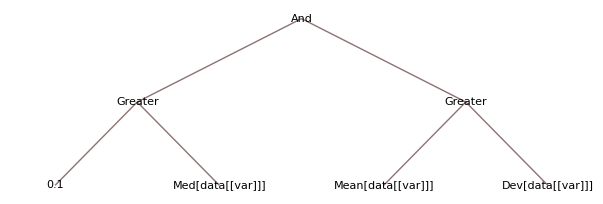

```mathematica
TreeForm[And[Greater["0.1","Med[data[[var]]]"],Greater["Mean[data[[var]]]","Dev[data[[var]]]"]]]
```

Now we need a method to generate a random tree model. We must have some restrictions so that numeric data can’t be given to the logic operators, since they are not compatible. We could restrict the models in a way that only allows a single Bool->Bool operator to be at the top and the intersection of any branch can only be Numeric->Bool operators, then the leaves can be any of the numeric operators.

To generate tree without them automatically evaluating, we need placeholders. So first we need to highlight all of the useful operators and their associated symbols.

(Operators | Symbols
And | α
Or | ω
Nand | ν
Nor | ñ
Xor | ξ
≥ | γ
> | ℽ
≤  | λ
< | ł
== | ϵ
!= | θ
Avg | μ
Med | β
Mn | ι
Mx | σ
Diff | ζ
Diff2 | ϕ
Diff3 | ς
GetRed | ž
GetGreen | ℷ
GetBlue | ℶ
Chng | τ
Dev | 🐈
data | δ
var | ρ)

Here we create the lists of operators

```mathematica
leafOps={μ,β,σ,ι,ζ,τ,🐈,Const,ϕ,ς,ž,ℷ, ℶ };
interOps={γ,ℽ,λ,ł,ϵ,θ};
nodeOps={α,ω,ν,ñ,ξ};
```

This function generates a random leaf node.

```mathematica
RandomLeaf[leafOps_]:=Block[{leaf},
leaf=RandomChoice[leafOps];
leaf=leaf[δ];
leaf
]
```

```mathematica
RandomLeaf[leafOps]
```

2.99791

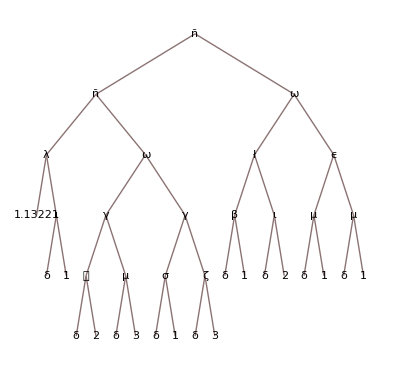

```mathematica
TreeForm@RandomBranch[nodeOps,interOps,leafOps,3]
```

```mathematica
RandomBranch[node_,inter_,leaves_]:=Block[{num,branch},
num=RandomInteger[{0,2}];
If[num==1,
branch=RandomChoice[node][RandomBranch[node,inter,leaves],RandomBranch[node,inter,leaves]]
,
branch=RandomChoice[inter][RandomLeaf[leaves],RandomLeaf[leaves]]
];
branch
]
```

```mathematica
RandomTr[node_,inter_,leaves_]:=Block[{depth,tree},
tree=RandomChoice[node][RandomBranch[node,inter,leaves],RandomBranch[node,inter,leaves]];
While[Depth[tree]>5,tree=RandomChoice[node][RandomBranch[node,inter,leaves],RandomBranch[node,inter,leaves]]];
tree
]
```

Now we have a method that can generate a random tree, next we will need operators for mutation and crossover.

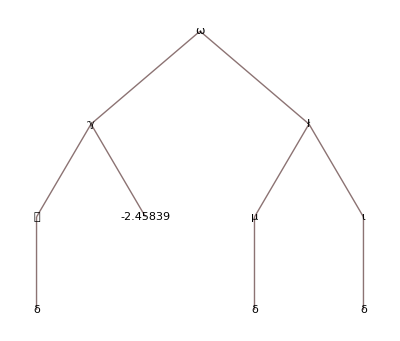

```mathematica
TreeForm[tree=RandomTr[nodeOps,interOps,leafOps,3]]
```

### Evaluate Models

```mathematica
TreeForm@tree
```

-Graphics-

```mathematica
Substitute[tree_]:=tree/.{α->And,ω->Or,ν->Nand,ñ->Nor,ξ->Xor,γ->GreaterEqual,ℽ->Greater,λ->LessEqual,ł->Less,ϵ->Equal,θ->Unequal}
```

```mathematica
EvaluateModel[tree:_?PolynomialQ,data_?VectorQ]:=(Substitute[tree]/.{μ->Avg,β->Med,ι->Mn,σ->Mx,ζ->Diff,τ->Chng,🐈->Dev,δ->data,ϕ->Diff2,ς->Diff3,ž->GetRed,ℷ->GetGreen, ℶ->GetBlue})
```

```mathematica
EvaluateModel[tree:_?PolynomialQ,data_?MatrixQ]:=(Substitute[tree]/.{μ->Avg,β->Med,ι->Mn,σ->Mx,ζ->Diff,τ->Chng,🐈->Dev,δ->#,ϕ->Diff2,ς->Diff3,ž->GetRed,ℷ->GetGreen, ℶ->GetBlue})&/@data
```

```mathematica
EvaluateModel[tree:_?PolynomialQ,data_?TensorQ]:=EvaluateModel[tree,#]&/@data
```

```mathematica
EvaluateModel[trees:_?VectorQ,data_]:=AllTrue[EvaluateModel[#,data]&/@trees,TrueQ]
```

```mathematica
ModelPhenotype[tree:_?PolynomialQ]:=TreeForm[tree/.{α->And,ω->Or,ν->Nand,ñ->Nor,ξ->Xor,γ->GreaterEqual,ℽ->Greater,λ->LessEqual,ł->Less,ϵ->Equal,θ->Unequal,μ->"Avg",β->"Med",ι->"Min",σ->"Max",ζ->"Diff",τ->"Chng",🐈->"Dev",ϕ->"Diff2",ς->"Diff3",ž->"GetRed",ℷ->"GetGreen", ℶ->"GetBlue"}]
```

```mathematica
ModelPhenotype[tree:_?VectorQ]:=ModelPhenotype[#]&/@tree
```

```mathematica
ViewPrediction[tree_?PolynomialQ,data_]:=Image[EvaluateModel[tree,data]/.{True->1,False->0}]
```

```mathematica
MatrixQ[{1,2,3}]
```

False

```mathematica
VectorQ[{1,2,3}]
```

True

```mathematica
EvaluateModel[tree,{{1,2,3},{5,4,3}}]
```

{True,True}

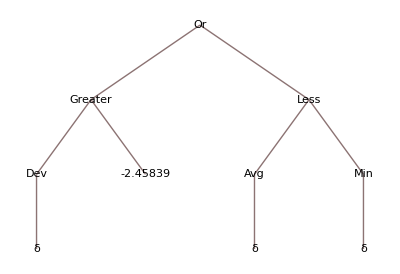

```mathematica
ModelPhenotype[tree]
```

(Operators | Symbols
And | α
Or | ω
Nand | ν
Nor | ñ
≥ | γ
> | ℽ
≤  | λ
< | ł
== | ϵ
Avg | μ
Med | β
Mn | ι
Mx | σ
Diff | ζ
Chng | τ
Dev | 🐈
data | δ
var | ρ)

### Genetic Operations

The first operator we will work on is the mutation operator. I’m thinking this would work best by simply replacing a branch. The challenge here is figuring out a method to efficiently navigate the trees to find a point for mutation.

```mathematica
Mutate[tree_,nodeOps_,interOps_,leafOps_]:=Block[
{list,sel,pos,newTree},
newTree=tree;
list=Join[nodeOps,interOps,leafOps];
sel=RandomChoice[list];
pos=Position[tree,sel];
Which[pos=={},newTree=tree,
Position[leafOps,sel]≠{},newTree[[RandomChoice[pos][[;;-2]]/.List->Sequence]]=RandomLeaf[leafOps],
Position[Join[nodeOps,interOps],sel]≠{},newTree[[RandomChoice[pos][[;;-2]]/.List->Sequence]]=RandomBranch[nodeOps,interOps,leafOps]];
newTree

]
```

New mutate function below (introduced 8/10/2023)

```mathematica
Mutate[tree_,nodeOps_,interOps_,leafOps_]:=Block[
	{list,sel,pos,newTree},
	newTree=tree;
	list=Join[nodeOps,interOps,leafOps];
	list=Cases[list,a_/;Position[tree,a]!={}];
	sel=RandomChoice[list];
	pos=Position[tree,sel];
	Which[pos=={},newTree=tree,
	Position[leafOps,sel]≠{},newTree[[RandomChoice[pos][[;;-2]]/.List->Sequence]]=RandomLeaf[leafOps],
	Position[Join[nodeOps,interOps],sel]≠{},newTree[[RandomChoice[pos][[;;-2]]/.List->Sequence]]=RandomBranch[nodeOps,interOps,leafOps]];
	newTree
]
```

```mathematica
sel=RandomChoice@Join[nodeOps,interOps,leafOps]
```

ζ

```mathematica
pos=Position[tree,sel]
```

{}

```mathematica
TreeForm@tree
```

-Graphics-

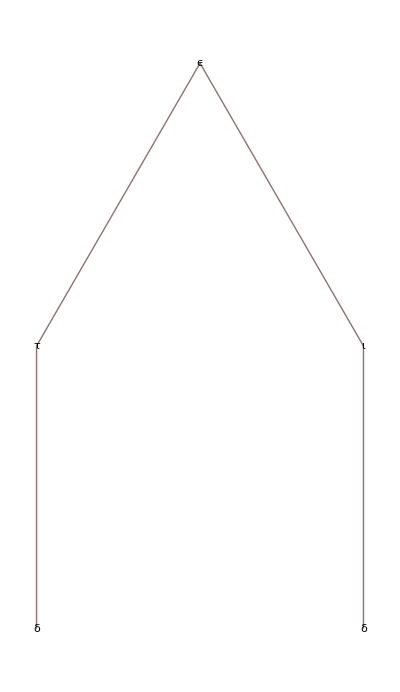

```mathematica
TreeForm@Mutate[tree,nodeOps,interOps,leafOps]
```

The next operator that we need is the crossover operator which will randomly select a branch in both trees and swap them.

```mathematica
CrossoverS[tree1_,tree2_,nodeOps_,interOps_,leafOps_]:=Block[
{list,newTree1,newTree2,sel1,sel2,pos1,pos2},
If[ContainsOnly[Position[tree1,#]&/@nodeOps,{{}}]||ContainsOnly[Position[tree2,#]&/@nodeOps,{{}}],
list=RandomChoice[{interOps,leafOps}],
list=RandomChoice[{nodeOps,interOps,leafOps}]];

newTree1=tree1;
newTree2=tree2;
While[Position[newTree1,sel1=RandomChoice[list]]=={}];
While[Position[newTree2,sel2=RandomChoice[list]]=={}];
pos1=RandomChoice[Position[tree1,sel1]][[;;-2]];
pos2=RandomChoice[Position[tree2,sel2]][[;;-2]];
newTree1[[pos1/.List->Sequence]]=tree2[[pos2/.List->Sequence]];
newTree2[[pos2/.List->Sequence]]=tree1[[pos1/.List->Sequence]];
{newTree1,newTree2}

]
```

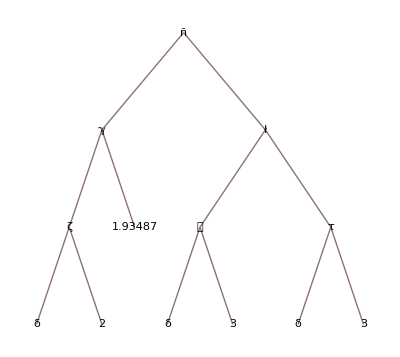
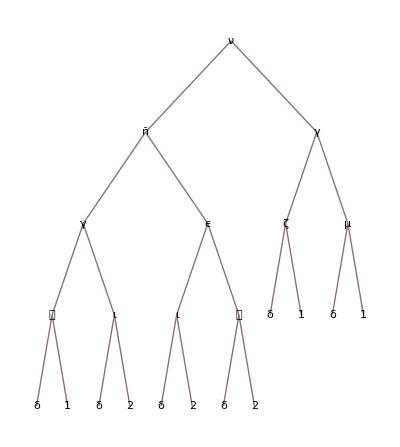

```mathematica
tree1=RandomTr[nodeOps,interOps,leafOps,3];
tree2=RandomTr[nodeOps,interOps,leafOps,3];
{TreeForm@tree1,TreeForm@tree2}
```

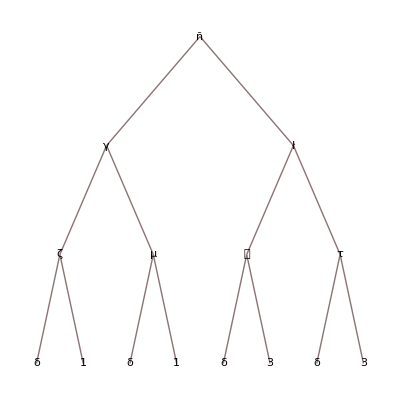
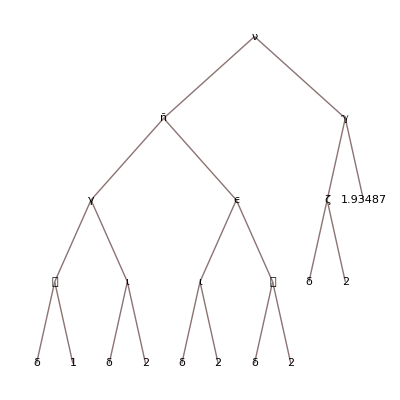

```mathematica
TreeForm/@CrossoverS[tree1,tree2,nodeOps,interOps,leafOps]
```

### Fitness

```mathematica
Fitness[tree_,data_,response_]:=Block[
{eval,fitness},
	If[Depth@data==3,
	eval=EvaluateModel[tree,data];
	fitness=Length[Cases[MapThread[#1==#2&,{response,eval}],True]];
	fitness=fitness/Length@data;
	,
	{fitness=Total[Table[Fitness[tree,data[[i]],response[[i]]],{i,1,Length@data}]],
	fitness=Max[{fitness,Length@response-fitness}]/Length@data}
	];

	fitness

]
```

```mathematica
RawFitness[tree_,data_,response_]:=Block[
{eval,fitness},
	If[Depth@data==3,
	eval=EvaluateModel[tree,data];
	fitness=Length[Cases[MapThread[#1==#2&,{response,eval}],True]];
	fitness=fitness/Length@data;
	,
	{fitness=Total[Table[RawFitness[tree,data[[i]],response[[i]]],{i,1,Length@data}]],
	fitness=fitness/Length@data}
	];

	fitness

]
```

```mathematica
Fitness[tree_,data_,response_]:=Block[
	{fitness},
	fitness=RawFitness[tree,data,response];
	Max[{fitness,1-fitness}]


]
```

```mathematica
Depth[{{1,2,3},{3,4,3},{3,3,3}}]
```

3

```mathematica
Depth[{{{1,2,3},{3,4,3},{3,3,3}}}]
```

4

```mathematica
Fitness[tree,{{{1,2,3},{3,4,3},{3,3,3}},{{1,2,3},{3,4,3},{3,3,3}}},{{False,False,True},{False,False,True}}]
```

2/3

```mathematica
10000*data[[120]]/data[[90]]
```

10678.6

```mathematica
Fitness[tree2,data,Range[90,120]]
```

10000

```mathematica
EvaluateModel[tree1,data,#]&/@Range[90,120]
```

{True,True,False,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,False,True,False,True,False,False,False,True,False,True,True,True,True}

```mathematica
TournamentSelection[models_]:=Block[
	{selectedModels},
	selectedModels=ReverseSortBy[models,Last][[1]][[1]]	
	
]
```

### EnsembleConfidence

Confidence is a key indicator to help determine if broadly a decision is agreed upon or not. Here we have a function that considers a set of Models and returns the percent confidence

```mathematica
EnsembleConfidence[Models_,data_]:=Block[{conf,out},
conf=EvaluateModel[#,data]&/@Models;
out=Max[N[Length[Cases[#,True]]/Length[#]],N[Length[Cases[#,False]]/Length[#]]]&/@Transpose[conf];
(*PercentForm@*);
out
]
```

```mathematica
EvaluateModel[#,{r,g,b}]&/@{tree1,tree2}
```

{False,True}

```mathematica
EnsembleConfidence[{tree1,tree2},{r,g,b}]
```

50%

### Evolution

Now to bring these functions together we need an evolution function.

```mathematica
Models={};
Do[AppendTo[Models,RandomTr[nodeOps,interOps,leafOps,3]],100];
```

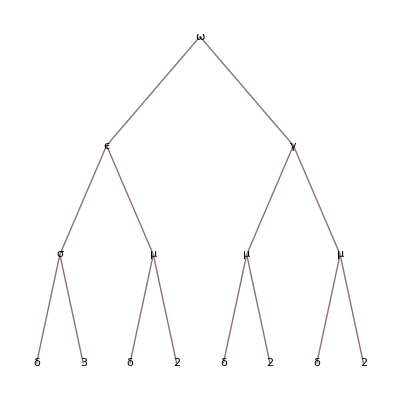

```mathematica
TreeForm@RandomChoice@Models
```

```mathematica
Options[Evolve]={
"NumModels"->30,
"Generations"->100,
"CrossoverRate"->0.4,
"MutationRate"->0.3,
"ElitistRate"->0.2,
"MaxDepth"->6,
"Fitness"->Fitness,
"InitialPopulation"->{}

};
```

```mathematica
Evolve[data_,response_,opts___?OptionQ]:=Evolve[data,response,nodeOps,interOps,leafOps,"NumModels"/.{opts}/.Options@Evolve,
"Generations"/.{opts}/.Options@Evolve,"CrossoverRate"/.{opts}/.Options@Evolve,"MutationRate"/.{opts}/.Options@Evolve,"ElitistRate"/.{opts}/.Options@Evolve,opts]
```

```mathematica
Evolve[data_,response_,nodeOps_,interOps_,leafOps_,numModels_,generations_,crossoverRate_,mutationRate_,elitistRate_,opts___?OptionQ]:=Block[
{models,tournamentSize,newModels,fit,child1,child2,sample,maxDepth,fitFunc,parent1,parent2},
tournamentSize=5;
gen=0;
models="InitialPopulation"/.{opts}/.Options@Evolve;
fitFunc="Fitness"/.{opts}/.Options@Evolve;
maxDepth="MaxDepth"/.{opts}/.Options@Evolve;
Do[AppendTo[models,RandomTr[nodeOps,interOps,leafOps]],numModels-Length@models];
Do[{
	gen+=1,
	newModels={},

	While[Length@newModels<crossoverRate*numModels,
		{
		sample=RandomSample[models,tournamentSize],
		fit={#,fitFunc[#,data,response]}&/@sample,
		(*fit=Transpose[ReverseSortBy[fit,Last]][[1]],*)
		parent1=TournamentSelection[fit],
		sample=RandomSample[models,tournamentSize],
		fit={#,fitFunc[#,data,response]}&/@sample,
		(*fit=Transpose[ReverseSortBy[fit,Last]][[1]],*)
		parent2=TournamentSelection[fit],		
		{child1,child2}=CrossoverS[parent1,parent2,nodeOps,interOps,leafOps],
		AppendTo[newModels,child1],
		AppendTo[newModels,child2]
		}
	],
	While[Length@newModels<crossoverRate*numModels+mutationRate*numModels,
		{
		sample=RandomSample[models,tournamentSize],
		fit={#,fitFunc[#,data,response]}&/@sample,
		(*fit=Transpose[ReverseSortBy[fit,Last]][[1]],*)
		parent1=TournamentSelection[fit],		
		AppendTo[newModels,Mutate[parent1,nodeOps,interOps,leafOps]]
		}
		
	],
	fit={#,fitFunc[#,data,response]}&/@models,
	newModels=Join[newModels,Transpose[ReverseSortBy[fit,Last]][[1]][[1;;Floor[elitistRate*numModels]]]],
	While[Length@newModels<numModels,AppendTo[newModels,RandomTr[nodeOps,interOps,leafOps]]],
	models=DeleteDuplicates@newModels,
	models=DeleteCases[models,a_ /;(Depth[a]>maxDepth)]



},
generations];
fit={#,fitFunc[#,data,response]}&/@models;
models=Transpose[ReverseSortBy[fit,Last]][[1]];
models
]
```

```mathematica
AlignModel[tree_,data_,response_]:=Block[{eval,fitness,newTree},
	newTree=tree;
	eval=EvaluateModel[tree,data];
	fitness=RawFitness[tree,data,response];(*Length[Cases[MapThread[#1==#2&,{response,eval}],True]]/Length[response];*)
	If[fitness<0.5,newTree=Not@tree];
	newTree]
```

```mathematica
ImageDiff[img1_,img2_]:=Total@Abs@Flatten[(img1/.{False->0,True->1})-(img2/.{False->0,True->1})]
```

```mathematica
Uncertainty[ensemble_,image_]:=Mean[ImageDiff[EvaluateModel[ensemble[[#[[1]]]],image],EvaluateModel[ensemble[[#[[2]]]],image]]&/@Subsets[Range[Length@ensemble],{2}]]
```

```mathematica
AlignModel[tree_,data_,response_]:=Block[{eval,fitness,newTree},
	newTree=tree;
	eval=EvaluateModel[tree,data];
	fitness=Length[Cases[MapThread[#1==#2&,{response,eval}],True]]/Length[response];
	If[fitness<0.5,newTree=Not@tree];
	newTree]
```